# Patch weight convergence test

### To ensure that our assumptions about how patch size relates to the values of patch weights, we will do some simulations: - for uniform weights, draw 10,000 patches with weights - sum each set of patch weights - check gross and average deviation, via or as n increases, we expect that average deviation will go to zero for [values of q]: - same process as constant weights above, but for 4 separate values of q

## Uniform weights

```mathematica
SeedRandom[123]; (* set seed so stuff is reproducible *)
(* number of repetitions per n *)
numReps = 1000;

(* geometric range of n values *)
nValues = Range[1000, 10000000, 100000];
Length[nValues]
(* simulate for each n *)
results = ParallelTable[
  Module[{samples, sums, sqDev, absDev},
    
    (* draw numReps samples of n uniform weights on (0, 2/n) *)
    samples = Table[
      Total@RandomReal[{0, 2/n}, n],
      {numReps}
    ];
    
    (* compute deviance metrics *)
    sqDev = Mean[(# - 1)^2 & /@ samples];
    absDev = Mean[Abs[# - 1] & /@ samples];
    
    <|
      "n" -> n,
      "MeanSum" -> Mean[samples],
      "SquaredDeviance" -> sqDev,
      "AbsoluteDeviance" -> absDev
    |>
  ],
  {n, nValues}
];

(* convert to a dataset for inspection *)
devTable = Dataset[results]
```

100

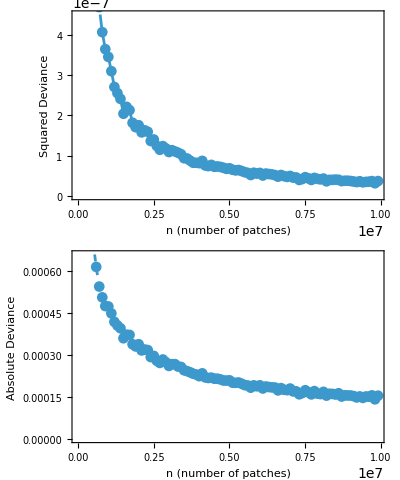

```mathematica
(* extract x and y values *)
squaredPoints = {#["n"], #["SquaredDeviance"]} & /@ results;
absolutePoints = {#["n"], #["AbsoluteDeviance"]} & /@ results;

(* top panel: squared deviance *)
sqPlot = ListPlot[
  squaredPoints,
  PlotStyle -> Automatic,
  Frame -> True,
  FrameLabel -> {"n (number of patches)", "Squared Deviance"},
  PlotMarkers -> Automatic,
  Joined -> True
];

(* bottom panel: absolute deviance *)
absPlot = ListPlot[
  absolutePoints,
  PlotStyle -> Dashed,
  Frame -> True,
  FrameLabel -> {"n (number of patches)", "Absolute Deviance"},
  PlotMarkers -> Automatic,
  Joined -> True
];

(* combine plots *)
GraphicsGrid[{{sqPlot}, {absPlot}}, Spacings -> {0, 2}]
```

## Uniform weights with q

```mathematica
(* number of repetitions *)
numReps = 1000;

(* geometric range of n values *)
nValues = Range[1000, 10000000, 100000];

(* main simulation loop *)
landscapeVarianceResults = ParallelTable[
  Module[{qVals, qResults},
   (* define q values for this specific n *)
    qVals = Range[0, 1/n, (1/n)/2];  (* 3 values: 0, 1/(2n), 1/n *)

    qResults = Table[
      Module[{samples, sums, sqDev, absDev},
        samples = Table[
          Total@RandomReal[{1/n - q, 1/n + q}, n],
          {numReps}
        ];
        sqDev = Mean[(# - 1)^2 & /@ samples];
        absDev = Mean[Abs[# - 1] & /@ samples];
        <|
          "n" -> n,
          "q" -> q,
          "MeanSum" -> Mean[samples],
          "SquaredDeviance" -> sqDev,
          "AbsoluteDeviance" -> absDev
        |>
      ],
      {q, qVals}
    ];
    qResults
  ],
  {n, nValues}
];

(* flatten results *)
landscapeVarianceResultsFlat = Flatten[landscapeVarianceResults, 1];
devDS = Dataset[landscapeVarianceResultsFlat]
```

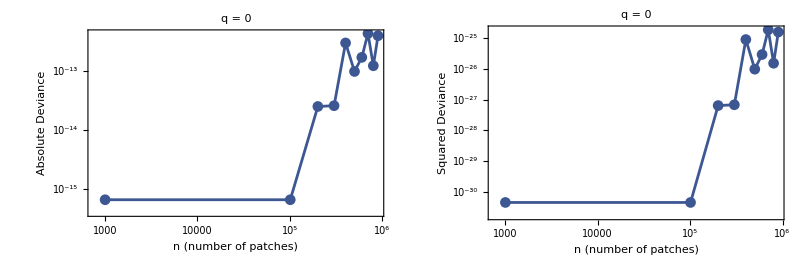

```mathematica
qColors = AssociationThread[
  qList -> ColorData["DarkRainbow"] /@ Rescale[Range[Length[qList]]]
];

plotsByQ = Table[
  Module[
    {
      thisQ = q,
      subdata = Select[landscapeVarianceResultsFlat, #q == q &],
      color = qColors[q],
      sortedAbs, sortedSq, absPlot, sqPlot
    },
    
    sortedAbs = SortBy[{#n, #AbsoluteDeviance} & /@ subdata, First];
    sortedSq = SortBy[{#n, #SquaredDeviance} & /@ subdata, First];
    
    absPlot = ListLogLogPlot[
      {sortedAbs},
      PlotStyle -> {color, Thick},
      PlotMarkers -> Automatic,
      Frame -> True,
      FrameLabel -> {"n (number of patches)", 
                     "Absolute Deviance"},
      PlotLabel -> Row[{"q = ", NumberForm[q, 4]}],
      Joined -> True
    ];
    
    sqPlot = ListLogLogPlot[
      {sortedSq},
      PlotStyle -> {color, Thick},
      PlotMarkers -> Automatic,
      Frame -> True,
      FrameLabel -> {"n (number of patches)", 
                     "Squared Deviance"},
      PlotLabel -> Row[{"q = ", NumberForm[q, 4]}],
      Joined -> True
    ];
    
    {absPlot, sqPlot}
  ],
  {q, qList}
];
GraphicsGrid[plotsByQ, Spacings -> {0.5, 1}]
```